# Elementary Functions

Loading the package

```mathematica
SetDirectory[NotebookDirectory[]];
<<ChisholmD.wl
```

ChisholmD.wl 1.0
Authors : Souvik Bera & Tanay Pathak

### 1. Exp[(x+y)/2]

```mathematica
CaExp0=Block[{order=6},ChisholmD[Normal[Series[Exp[(x+y)/2],{x,0,50},{y,0,50}]],{0,0,order},{x,y}]];
valuesexp=
Flatten[Join[ {{"{x,y}", "CA" , "Function","% Error"}},Flatten[Table[{{x,y},N[CaExp0,10],N[Exp[(x+y)/2],10],N[Abs[(CaExp0-Exp[(x+y)/2])/Exp[(x+y)/2]]100,5]},{x,0,10},{y,0,10}],1]],{1}];
Labeled[Grid[valuesexp,Frame-> All],"Table:1a",Top,LabelStyle->Red]
```

{x,y} | CA | Function | % Error
{0,0} | 1. | 1. | 0
{0,1} | 1.648721271 | 1.648721271 | 2.132×10^-15
{0,2} | 2.718281828 | 2.718281828 | 1.7725×10^-11
{0,3} | 4.48168907 | 4.48168907 | 3.5354×10^-9
{0,4} | 7.389056088 | 7.389056099 | 1.54×10^-7
{0,5} | 12.1824936 | 12.18249396 | 2.927×10^-6
{0,6} | 20.08553029 | 20.08553692 | 0.000033036
{0,7} | 33.11536554 | 33.11545196 | 0.00026096
{0,8} | 54.59728122 | 54.59815003 | 0.0015913
{0,9} | 90.00994916 | 90.0171313 | 0.0079786
{0,10} | 148.3622 | 148.4131591 | 0.034336
{1,0} | 1.648721271 | 1.648721271 | 2.132×10^-15
{1,1} | 2.718281828 | 2.718281828 | 4.2641×10^-15
{1,2} | 4.48168907 | 4.48168907 | 1.7727×10^-11
{1,3} | 7.389056099 | 7.389056099 | 3.5354×10^-9
{1,4} | 12.18249394 | 12.18249396 | 1.54×10^-7
{1,5} | 20.08553634 | 20.08553692 | 2.927×10^-6
{1,6} | 33.11544102 | 33.11545196 | 0.000033036
{1,7} | 54.59800756 | 54.59815003 | 0.00026096
{1,8} | 90.01569888 | 90.0171313 | 0.0015913
{1,9} | 148.4013178 | 148.4131591 | 0.0079786
{1,10} | 244.6079149 | 244.6919323 | 0.034336
{2,0} | 2.718281828 | 2.718281828 | 1.7725×10^-11
{2,1} | 4.48168907 | 4.48168907 | 1.7727×10^-11
{2,2} | 7.389056099 | 7.389056099 | 3.5451×10^-11
{2,3} | 12.18249396 | 12.18249396 | 3.5531×10^-9
{2,4} | 20.08553689 | 20.08553692 | 1.5402×10^-7
{2,5} | 33.11545099 | 33.11545196 | 2.927×10^-6
{2,6} | 54.598132 | 54.59815003 | 0.000033036
{2,7} | 90.01689639 | 90.0171313 | 0.00026096
{2,8} | 148.4107974 | 148.4131591 | 0.0015913
{2,9} | 244.6724092 | 244.6919323 | 0.0079786
{2,10} | 403.2902722 | 403.4287935 | 0.034336
{3,0} | 4.48168907 | 4.48168907 | 3.5354×10^-9
{3,1} | 7.389056099 | 7.389056099 | 3.5354×10^-9
{3,2} | 12.18249396 | 12.18249396 | 3.5531×10^-9
{3,3} | 20.08553692 | 20.08553692 | 7.0708×10^-9
{3,4} | 33.11545191 | 33.11545196 | 1.5754×10^-7
{3,5} | 54.59814843 | 54.59815003 | 2.9306×10^-6
{3,6} | 90.01710156 | 90.0171313 | 0.000033039
{3,7} | 148.4127718 | 148.4131591 | 0.00026096
{3,8} | 244.6880385 | 244.6919323 | 0.0015913
{3,9} | 403.3966054 | 403.4287935 | 0.0079786
{3,10} | 664.9132501 | 665.141633 | 0.034336
{4,0} | 7.389056088 | 7.389056099 | 1.54×10^-7
{4,1} | 12.18249394 | 12.18249396 | 1.54×10^-7
{4,2} | 20.08553689 | 20.08553692 | 1.5402×10^-7
{4,3} | 33.11545191 | 33.11545196 | 1.5754×10^-7
{4,4} | 54.59814986 | 54.59815003 | 3.0801×10^-7
{4,5} | 90.01712853 | 90.0171313 | 3.081×10^-6
{4,6} | 148.4131098 | 148.4131591 | 0.00003319
{4,7} | 244.6912933 | 244.6919323 | 0.00026111
{4,8} | 403.4223732 | 403.4287935 | 0.0015914
{4,9} | 665.0885628 | 665.141633 | 0.0079788
{4,10} | 1096.256617 | 1096.633158 | 0.034336
{5,0} | 12.1824936 | 12.18249396 | 2.927×10^-6
{5,1} | 20.08553634 | 20.08553692 | 2.927×10^-6
{5,2} | 33.11545099 | 33.11545196 | 2.927×10^-6
{5,3} | 54.59814843 | 54.59815003 | 2.9306×10^-6
{5,4} | 90.01712853 | 90.0171313 | 3.081×10^-6
{5,5} | 148.4131504 | 148.4131591 | 5.854×10^-6
{5,6} | 244.6918443 | 244.6919323 | 0.000035963
{5,7} | 403.4277289 | 403.4287935 | 0.00026388
{5,8} | 665.1310293 | 665.141633 | 0.0015942
{5,9} | 1096.54563 | 1096.633158 | 0.0079816
{5,10} | 1807.421552 | 1808.042414 | 0.034339
{6,0} | 20.08553029 | 20.08553692 | 0.000033036
{6,1} | 33.11544102 | 33.11545196 | 0.000033036
{6,2} | 54.598132 | 54.59815003 | 0.000033036
{6,3} | 90.01710156 | 90.0171313 | 0.000033039
{6,4} | 148.4131098 | 148.4131591 | 0.00003319
{6,5} | 244.6918443 | 244.6919323 | 0.000035963
{6,6} | 403.4285269 | 403.4287935 | 0.000066071
{6,7} | 665.1396776 | 665.141633 | 0.00029399
{6,8} | 1096.615346 | 1096.633158 | 0.0016243
{6,9} | 1807.89756 | 1808.042414 | 0.0080117
{6,10} | 2979.933461 | 2980.957987 | 0.034369
{7,0} | 33.11536554 | 33.11545196 | 0.00026096
{7,1} | 54.59800756 | 54.59815003 | 0.00026096
{7,2} | 90.01689639 | 90.0171313 | 0.00026096
{7,3} | 148.4127718 | 148.4131591 | 0.00026096
{7,4} | 244.6912933 | 244.6919323 | 0.00026111
{7,5} | 403.4277289 | 403.4287935 | 0.00026388
{7,6} | 665.1396776 | 665.141633 | 0.00029399
{7,7} | 1096.627435 | 1096.633158 | 0.00052191
{7,8} | 1808.008925 | 1808.042414 | 0.0018522
{7,9} | 2980.712369 | 2980.957987 | 0.0082396
{7,10} | 4913.068485 | 4914.76884 | 0.034597
{8,0} | 54.59728122 | 54.59815003 | 0.0015913
{8,1} | 90.01569888 | 90.0171313 | 0.0015913
{8,2} | 148.4107974 | 148.4131591 | 0.0015913
{8,3} | 244.6880385 | 244.6919323 | 0.0015913
{8,4} | 403.4223732 | 403.4287935 | 0.0015914
{8,5} | 665.1310293 | 665.141633 | 0.0015942
{8,6} | 1096.615346 | 1096.633158 | 0.0016243
{8,7} | 1808.008925 | 1808.042414 | 0.0018522
{8,8} | 2980.863117 | 2980.957987 | 0.0031825
{8,9} | 4914.298507 | 4914.76884 | 0.0095698
{8,10} | 8100.172755 | 8103.083928 | 0.035927
{9,0} | 90.00994916 | 90.0171313 | 0.0079786
{9,1} | 148.4013178 | 148.4131591 | 0.0079786
{9,2} | 244.6724092 | 244.6919323 | 0.0079786
{9,3} | 403.3966054 | 403.4287935 | 0.0079786
{9,4} | 665.0885628 | 665.141633 | 0.0079788
{9,5} | 1096.54563 | 1096.633158 | 0.0079816
{9,6} | 1807.89756 | 1808.042414 | 0.0080117
{9,7} | 2980.712369 | 2980.957987 | 0.0082396
{9,8} | 4914.298507 | 4914.76884 | 0.0095698
{9,9} | 8101.790948 | 8103.083928 | 0.015957
{9,10} | 13354.07408 | 13359.72683 | 0.042312
{10,0} | 148.3622 | 148.4131591 | 0.034336
{10,1} | 244.6079149 | 244.6919323 | 0.034336
{10,2} | 403.2902722 | 403.4287935 | 0.034336
{10,3} | 664.9132501 | 665.141633 | 0.034336
{10,4} | 1096.256617 | 1096.633158 | 0.034336
{10,5} | 1807.421552 | 1808.042414 | 0.034339
{10,6} | 2979.933461 | 2980.957987 | 0.034369
{10,7} | 4913.068485 | 4914.76884 | 0.034597
{10,8} | 8100.172755 | 8103.083928 | 0.035927
{10,9} | 13354.07408 | 13359.72683 | 0.042312
{10,10} | 22011.34238 | 22026.46579 | 0.06866Table:1a

Evaluating the CA around (5,5)

Order= 5

```mathematica
CaExp555=Block[{order=5},Chrisholm[Normal[Series[Exp[(x+y)/2],{x,0,50},{y,0,50}]],{5,5,order},{x,y}]];
valuesexp555=Flatten[Join[ {{"{x,y}", "CA" , "Function","% Error"}},Flatten[Table[{{x,y},N[CaExp555,10],N[Exp[(x+y)/2],10],N[Abs[(CaExp555-Exp[(x+y)/2])/Exp[(x+y)/2]]100,5]},{x,0,10},{y,0,10}],1]],{1}];
Labeled[Grid[valuesexp555,Frame-> All],"Table:1b",Top,LabelStyle->Red]
```

{x,y} | CA | Function | % Error
{0,0} | 0.9999945165 | 1. | 0.00054835
{0,1} | 1.648716382 | 1.648721271 | 0.00029653
{0,2} | 2.718274351 | 2.718281828 | 0.00027508
{0,3} | 4.481676782 | 4.48168907 | 0.00027419
{0,4} | 7.38903584 | 7.389056099 | 0.00027418
{0,5} | 12.18246056 | 12.18249396 | 0.00027418
{0,6} | 20.08548185 | 20.08553692 | 0.00027418
{0,7} | 33.11536117 | 33.11545196 | 0.00027417
{0,8} | 54.59800083 | 54.59815003 | 0.00027327
{0,9} | 90.01690462 | 90.0171313 | 0.00025182
{0,10} | 148.4131591 | 148.4131591 | 1.9057×10^-35
{1,0} | 1.648716382 | 1.648721271 | 0.00029653
{1,1} | 2.718280613 | 2.718281828 | 0.00004471
{1,2} | 4.481688028 | 4.48168907 | 0.000023262
{1,3} | 7.389054446 | 7.389056099 | 0.000022365
{1,4} | 12.18249124 | 12.18249396 | 0.000022355
{1,5} | 20.08553243 | 20.08553692 | 0.000022355
{1,6} | 33.11544456 | 33.11545196 | 0.000022355
{1,7} | 54.59813783 | 54.59815003 | 0.000022345
{1,8} | 90.01711199 | 90.0171313 | 0.000021449
{1,9} | 148.4131591 | 148.4131591 | 1.9887×10^-36
{1,10} | 244.6925485 | 244.6919323 | 0.00025182
{2,0} | 2.718274351 | 2.718281828 | 0.00027508
{2,1} | 4.481688028 | 4.48168907 | 0.000023262
{2,2} | 7.389055965 | 7.389056099 | 1.8129×10^-6
{2,3} | 12.18249385 | 12.18249396 | 9.1662×10^-7
{2,4} | 20.08553674 | 20.08553692 | 9.0645×10^-7
{2,5} | 33.11545166 | 33.11545196 | 9.0645×10^-7
{2,6} | 54.59814954 | 54.59815003 | 9.0644×10^-7
{2,7} | 90.01713049 | 90.0171313 | 8.9627×10^-7
{2,8} | 148.4131591 | 148.4131591 | 1.146×10^-37
{2,9} | 244.6919847 | 244.6919323 | 0.000021449
{2,10} | 403.4298959 | 403.4287935 | 0.00027327
{3,0} | 4.481676782 | 4.48168907 | 0.00027419
{3,1} | 7.389054446 | 7.389056099 | 0.000022365
{3,2} | 12.18249385 | 12.18249396 | 9.1662×10^-7
{3,3} | 20.08553692 | 20.08553692 | 2.0355×10^-8
{3,4} | 33.11545196 | 33.11545196 | 1.0182×10^-8
{3,5} | 54.59815003 | 54.59815003 | 1.0177×10^-8
{3,6} | 90.01713129 | 90.0171313 | 1.0173×10^-8
{3,7} | 148.4131591 | 148.4131591 | 2.3547×10^-39
{3,8} | 244.6919345 | 244.6919323 | 8.9627×10^-7
{3,9} | 403.4288836 | 403.4287935 | 0.000022345
{3,10} | 665.1434566 | 665.141633 | 0.00027417
{4,0} | 7.38903584 | 7.389056099 | 0.00027418
{4,1} | 12.18249124 | 12.18249396 | 0.000022355
{4,2} | 20.08553674 | 20.08553692 | 9.0645×10^-7
{4,3} | 33.11545196 | 33.11545196 | 1.0182×10^-8
{4,4} | 54.59815003 | 54.59815003 | 9.7655×10^-12
{4,5} | 90.0171313 | 90.0171313 | 4.8828×10^-12
{4,6} | 148.4131591 | 148.4131591 | 6.4652×10^-42
{4,7} | 244.6919323 | 244.6919323 | 1.0173×10^-8
{4,8} | 403.4287971 | 403.4287935 | 9.0644×10^-7
{4,9} | 665.1417817 | 665.141633 | 0.000022355
{4,10} | 1096.636165 | 1096.633158 | 0.00027418
{5,0} | 12.18246056 | 12.18249396 | 0.00027418
{5,1} | 20.08553243 | 20.08553692 | 0.000022355
{5,2} | 33.11545166 | 33.11545196 | 9.0645×10^-7
{5,3} | 54.59815003 | 54.59815003 | 1.0177×10^-8
{5,4} | 90.0171313 | 90.0171313 | 4.8828×10^-12
{5,5} | 148.4131591 | 148.4131591 | 2.1926×10^-45
{5,6} | 244.6919323 | 244.6919323 | 4.8828×10^-12
{5,7} | 403.4287935 | 403.4287935 | 1.0177×10^-8
{5,8} | 665.1416391 | 665.141633 | 9.0645×10^-7
{5,9} | 1096.633404 | 1096.633158 | 0.000022355
{5,10} | 1808.047372 | 1808.042414 | 0.00027418
{6,0} | 20.08548185 | 20.08553692 | 0.00027418
{6,1} | 33.11544456 | 33.11545196 | 0.000022355
{6,2} | 54.59814954 | 54.59815003 | 9.0644×10^-7
{6,3} | 90.01713129 | 90.0171313 | 1.0173×10^-8
{6,4} | 148.4131591 | 148.4131591 | 6.4652×10^-42
{6,5} | 244.6919323 | 244.6919323 | 4.8828×10^-12
{6,6} | 403.4287935 | 403.4287935 | 9.7655×10^-12
{6,7} | 665.1416331 | 665.141633 | 1.0182×10^-8
{6,8} | 1096.633168 | 1096.633158 | 9.0645×10^-7
{6,9} | 1808.042819 | 1808.042414 | 0.000022355
{6,10} | 2980.96616 | 2980.957987 | 0.00027418
{7,0} | 33.11536117 | 33.11545196 | 0.00027417
{7,1} | 54.59813783 | 54.59815003 | 0.000022345
{7,2} | 90.01713049 | 90.0171313 | 8.9627×10^-7
{7,3} | 148.4131591 | 148.4131591 | 2.3547×10^-39
{7,4} | 244.6919323 | 244.6919323 | 1.0173×10^-8
{7,5} | 403.4287935 | 403.4287935 | 1.0177×10^-8
{7,6} | 665.1416331 | 665.141633 | 1.0182×10^-8
{7,7} | 1096.633159 | 1096.633158 | 2.0355×10^-8
{7,8} | 1808.042431 | 1808.042414 | 9.1662×10^-7
{7,9} | 2980.958654 | 2980.957987 | 0.000022365
{7,10} | 4914.782316 | 4914.76884 | 0.00027419
{8,0} | 54.59800083 | 54.59815003 | 0.00027327
{8,1} | 90.01711199 | 90.0171313 | 0.000021449
{8,2} | 148.4131591 | 148.4131591 | 1.146×10^-37
{8,3} | 244.6919345 | 244.6919323 | 8.9627×10^-7
{8,4} | 403.4287971 | 403.4287935 | 9.0644×10^-7
{8,5} | 665.1416391 | 665.141633 | 9.0645×10^-7
{8,6} | 1096.633168 | 1096.633158 | 9.0645×10^-7
{8,7} | 1808.042431 | 1808.042414 | 9.1662×10^-7
{8,8} | 2980.958041 | 2980.957987 | 1.8129×10^-6
{8,9} | 4914.769984 | 4914.76884 | 0.000023262
{8,10} | 8103.106218 | 8103.083928 | 0.00027508
{9,0} | 90.01690462 | 90.0171313 | 0.00025182
{9,1} | 148.4131591 | 148.4131591 | 1.9887×10^-36
{9,2} | 244.6919847 | 244.6919323 | 0.000021449
{9,3} | 403.4288836 | 403.4287935 | 0.000022345
{9,4} | 665.1417817 | 665.141633 | 0.000022355
{9,5} | 1096.633404 | 1096.633158 | 0.000022355
{9,6} | 1808.042819 | 1808.042414 | 0.000022355
{9,7} | 2980.958654 | 2980.957987 | 0.000022365
{9,8} | 4914.769984 | 4914.76884 | 0.000023262
{9,9} | 8103.08755 | 8103.083928 | 0.00004471
{9,10} | 13359.76645 | 13359.72683 | 0.00029653
{10,0} | 148.4131591 | 148.4131591 | 1.9057×10^-35
{10,1} | 244.6925485 | 244.6919323 | 0.00025182
{10,2} | 403.4298959 | 403.4287935 | 0.00027327
{10,3} | 665.1434566 | 665.141633 | 0.00027417
{10,4} | 1096.636165 | 1096.633158 | 0.00027418
{10,5} | 1808.047372 | 1808.042414 | 0.00027418
{10,6} | 2980.96616 | 2980.957987 | 0.00027418
{10,7} | 4914.782316 | 4914.76884 | 0.00027419
{10,8} | 8103.106218 | 8103.083928 | 0.00027508
{10,9} | 13359.76645 | 13359.72683 | 0.00029653
{10,10} | 22026.58658 | 22026.46579 | 0.00054836Table:1b

Order= 7

```mathematica
CaExp556=Block[{order=7},Chrisholm[Normal[Series[Exp[(x+y)/2],{x,0,50},{y,0,50}]],{5,5,order},{x,y}]];
valuesexp556=Flatten[Join[ {{"{x,y}", "CA" , "Function","% Error"}},Flatten[Table[{{x,y},N[CaExp556,10],N[Exp[(x+y)/2],10],N[Abs[(CaExp556-Exp[(x+y)/2])/Exp[(x+y)/2]]100,5]},{x,0,10},{y,0,10}],1]],{1}];
Labeled[Grid[valuesexp556,Frame-> All],"Table:1c",Top,LabelStyle->Red]
```

{x,y} | CA | Function | % Error
{0,0} | 0.9999999995 | 1. | 4.6127×10^-8
{0,1} | 1.64872127 | 1.648721271 | 2.3845×10^-8
{0,2} | 2.718281828 | 2.718281828 | 2.3074×10^-8
{0,3} | 4.481689069 | 4.48168907 | 2.3063×10^-8
{0,4} | 7.389056097 | 7.389056099 | 2.3063×10^-8
{0,5} | 12.18249396 | 12.18249396 | 2.3063×10^-8
{0,6} | 20.08553692 | 20.08553692 | 2.3063×10^-8
{0,7} | 33.11545195 | 33.11545196 | 2.3063×10^-8
{0,8} | 54.59815002 | 54.59815003 | 2.3053×10^-8
{0,9} | 90.01713128 | 90.0171313 | 2.2282×10^-8
{0,10} | 148.4131591 | 148.4131591 | 1.4195×10^-33
{1,0} | 1.64872127 | 1.648721271 | 2.3845×10^-8
{1,1} | 2.718281828 | 2.718281828 | 1.5625×10^-9
{1,2} | 4.48168907 | 4.48168907 | 7.9141×10^-10
{1,3} | 7.389056099 | 7.389056099 | 7.813×10^-10
{1,4} | 12.18249396 | 12.18249396 | 7.8127×10^-10
{1,5} | 20.08553692 | 20.08553692 | 7.8127×10^-10
{1,6} | 33.11545196 | 33.11545196 | 7.8127×10^-10
{1,7} | 54.59815003 | 54.59815003 | 7.8125×10^-10
{1,8} | 90.0171313 | 90.0171313 | 7.7114×10^-10
{1,9} | 148.4131591 | 148.4131591 | 6.5248×10^-35
{1,10} | 244.6919323 | 244.6919323 | 2.2282×10^-8
{2,0} | 2.718281828 | 2.718281828 | 2.3074×10^-8
{2,1} | 4.48168907 | 4.48168907 | 7.9141×10^-10
{2,2} | 7.389056099 | 7.389056099 | 2.0273×10^-11
{2,3} | 12.18249396 | 12.18249396 | 1.0159×10^-11
{2,4} | 20.08553692 | 20.08553692 | 1.0136×10^-11
{2,5} | 33.11545196 | 33.11545196 | 1.0136×10^-11
{2,6} | 54.59815003 | 54.59815003 | 1.0136×10^-11
{2,7} | 90.0171313 | 90.0171313 | 1.0114×10^-11
{2,8} | 148.4131591 | 148.4131591 | 1.3631×10^-36
{2,9} | 244.6919323 | 244.6919323 | 7.7114×10^-10
{2,10} | 403.4287936 | 403.4287935 | 2.3053×10^-8
{3,0} | 4.481689069 | 4.48168907 | 2.3063×10^-8
{3,1} | 7.389056099 | 7.389056099 | 7.813×10^-10
{3,2} | 12.18249396 | 12.18249396 | 1.0159×10^-11
{3,3} | 20.08553692 | 20.08553692 | 4.5326×10^-14
{3,4} | 33.11545196 | 33.11545196 | 2.2664×10^-14
{3,5} | 54.59815003 | 54.59815003 | 2.2663×10^-14
{3,6} | 90.0171313 | 90.0171313 | 2.2662×10^-14
{3,7} | 148.4131591 | 148.4131591 | 8.0436×10^-39
{3,8} | 244.6919323 | 244.6919323 | 1.0114×10^-11
{3,9} | 403.4287935 | 403.4287935 | 7.8125×10^-10
{3,10} | 665.1416332 | 665.141633 | 2.3063×10^-8
{4,0} | 7.389056097 | 7.389056099 | 2.3063×10^-8
{4,1} | 12.18249396 | 12.18249396 | 7.8127×10^-10
{4,2} | 20.08553692 | 20.08553692 | 1.0136×10^-11
{4,3} | 33.11545196 | 33.11545196 | 2.2664×10^-14
{4,4} | 54.59815003 | 54.59815003 | 1.3658×10^-18
{4,5} | 90.0171313 | 90.0171313 | 6.8288×10^-19
{4,6} | 148.4131591 | 148.4131591 | 7.2992×10^-42
{4,7} | 244.6919323 | 244.6919323 | 2.2662×10^-14
{4,8} | 403.4287935 | 403.4287935 | 1.0136×10^-11
{4,9} | 665.141633 | 665.141633 | 7.8127×10^-10
{4,10} | 1096.633159 | 1096.633158 | 2.3063×10^-8
{5,0} | 12.18249396 | 12.18249396 | 2.3063×10^-8
{5,1} | 20.08553692 | 20.08553692 | 7.8127×10^-10
{5,2} | 33.11545196 | 33.11545196 | 1.0136×10^-11
{5,3} | 54.59815003 | 54.59815003 | 2.2663×10^-14
{5,4} | 90.0171313 | 90.0171313 | 6.8288×10^-19
{5,5} | 148.4131591 | 148.4131591 | 2.1926×10^-45
{5,6} | 244.6919323 | 244.6919323 | 6.8288×10^-19
{5,7} | 403.4287935 | 403.4287935 | 2.2663×10^-14
{5,8} | 665.141633 | 665.141633 | 1.0136×10^-11
{5,9} | 1096.633158 | 1096.633158 | 7.8127×10^-10
{5,10} | 1808.042415 | 1808.042414 | 2.3063×10^-8
{6,0} | 20.08553692 | 20.08553692 | 2.3063×10^-8
{6,1} | 33.11545196 | 33.11545196 | 7.8127×10^-10
{6,2} | 54.59815003 | 54.59815003 | 1.0136×10^-11
{6,3} | 90.0171313 | 90.0171313 | 2.2662×10^-14
{6,4} | 148.4131591 | 148.4131591 | 7.2992×10^-42
{6,5} | 244.6919323 | 244.6919323 | 6.8288×10^-19
{6,6} | 403.4287935 | 403.4287935 | 1.3658×10^-18
{6,7} | 665.141633 | 665.141633 | 2.2664×10^-14
{6,8} | 1096.633158 | 1096.633158 | 1.0136×10^-11
{6,9} | 1808.042414 | 1808.042414 | 7.8127×10^-10
{6,10} | 2980.957988 | 2980.957987 | 2.3063×10^-8
{7,0} | 33.11545195 | 33.11545196 | 2.3063×10^-8
{7,1} | 54.59815003 | 54.59815003 | 7.8125×10^-10
{7,2} | 90.0171313 | 90.0171313 | 1.0114×10^-11
{7,3} | 148.4131591 | 148.4131591 | 8.0436×10^-39
{7,4} | 244.6919323 | 244.6919323 | 2.2662×10^-14
{7,5} | 403.4287935 | 403.4287935 | 2.2663×10^-14
{7,6} | 665.141633 | 665.141633 | 2.2664×10^-14
{7,7} | 1096.633158 | 1096.633158 | 4.5326×10^-14
{7,8} | 1808.042414 | 1808.042414 | 1.0159×10^-11
{7,9} | 2980.957987 | 2980.957987 | 7.813×10^-10
{7,10} | 4914.768841 | 4914.76884 | 2.3063×10^-8
{8,0} | 54.59815002 | 54.59815003 | 2.3053×10^-8
{8,1} | 90.0171313 | 90.0171313 | 7.7114×10^-10
{8,2} | 148.4131591 | 148.4131591 | 1.3631×10^-36
{8,3} | 244.6919323 | 244.6919323 | 1.0114×10^-11
{8,4} | 403.4287935 | 403.4287935 | 1.0136×10^-11
{8,5} | 665.141633 | 665.141633 | 1.0136×10^-11
{8,6} | 1096.633158 | 1096.633158 | 1.0136×10^-11
{8,7} | 1808.042414 | 1808.042414 | 1.0159×10^-11
{8,8} | 2980.957987 | 2980.957987 | 2.0273×10^-11
{8,9} | 4914.76884 | 4914.76884 | 7.9141×10^-10
{8,10} | 8103.083929 | 8103.083928 | 2.3074×10^-8
{9,0} | 90.01713128 | 90.0171313 | 2.2282×10^-8
{9,1} | 148.4131591 | 148.4131591 | 6.5248×10^-35
{9,2} | 244.6919323 | 244.6919323 | 7.7114×10^-10
{9,3} | 403.4287935 | 403.4287935 | 7.8125×10^-10
{9,4} | 665.141633 | 665.141633 | 7.8127×10^-10
{9,5} | 1096.633158 | 1096.633158 | 7.8127×10^-10
{9,6} | 1808.042414 | 1808.042414 | 7.8127×10^-10
{9,7} | 2980.957987 | 2980.957987 | 7.813×10^-10
{9,8} | 4914.76884 | 4914.76884 | 7.9141×10^-10
{9,9} | 8103.083928 | 8103.083928 | 1.5625×10^-9
{9,10} | 13359.72683 | 13359.72683 | 2.3845×10^-8
{10,0} | 148.4131591 | 148.4131591 | 1.4195×10^-33
{10,1} | 244.6919323 | 244.6919323 | 2.2282×10^-8
{10,2} | 403.4287936 | 403.4287935 | 2.3053×10^-8
{10,3} | 665.1416332 | 665.141633 | 2.3063×10^-8
{10,4} | 1096.633159 | 1096.633158 | 2.3063×10^-8
{10,5} | 1808.042415 | 1808.042414 | 2.3063×10^-8
{10,6} | 2980.957988 | 2980.957987 | 2.3063×10^-8
{10,7} | 4914.768841 | 4914.76884 | 2.3063×10^-8
{10,8} | 8103.083929 | 8103.083928 | 2.3074×10^-8
{10,9} | 13359.72683 | 13359.72683 | 2.3845×10^-8
{10,10} | 22026.4658 | 22026.46579 | 4.6127×10^-8Table:1c

### 2. Sin[(x+y)/2]

For this case we need to subtract 1 from the approximation so as to account for the assumption: C[0,0]=1

```mathematica
CaSin00=Block[{order=5},ChisholmD[1+Normal[Series[Sin[(x+y)/2],{x,0,2 order},{y,0,2 order}]],{0,0,order},{x,y}]-1];
valuesin00=Flatten[Join[ {{"{x,y}", "CA" , "Function","% Error"}},Flatten[Table[{{x,y},CaSin00,Sin[(x+y)/2],Abs[(CaSin00-Sin[(x+y)/2])/Sin[(x+y)/2]]100},{x,0.1,5.1},{y,0.1,5.1}],1]],{1}];
Labeled[Grid[valuesin00,Frame->All],"Table:2a",Top,LabelStyle->Red]//N
```

{x,y} | CA | Function | % Error
{0.1,0.1} | 0.0998334 | 0.0998334 | 1.66811×10^-13
{0.1,1.1} | 0.564642 | 0.564642 | 5.86042×10^-9
{0.1,2.1} | 0.891207 | 0.891207 | 4.34774×10^-6
{0.1,3.1} | 0.999576 | 0.999574 | 0.000260952
{0.1,4.1} | 0.86326 | 0.863209 | 0.00590776
{0.1,5.1} | 0.515996 | 0.515501 | 0.09586
{1.1,0.1} | 0.564642 | 0.564642 | 5.86034×10^-9
{1.1,1.1} | 0.891207 | 0.891207 | 4.42588×10^-7
{1.1,2.1} | 0.999574 | 0.999574 | 0.0000408881
{1.1,3.1} | 0.86322 | 0.863209 | 0.00124793
{1.1,4.1} | 0.515636 | 0.515501 | 0.0260649
{1.1,5.1} | 0.0425938 | 0.0415807 | 2.43664
{2.1,0.1} | 0.891207 | 0.891207 | 4.34774×10^-6
{2.1,1.1} | 0.999574 | 0.999574 | 0.0000408881
{2.1,2.1} | 0.863223 | 0.863209 | 0.00158725
{2.1,3.1} | 0.515674 | 0.515501 | 0.0335239
{2.1,4.1} | 0.0428111 | 0.0415807 | 2.95921
{2.1,5.1} | -0.436473 | -0.44252 | 1.36649
{3.1,0.1} | 0.999576 | 0.999574 | 0.000260952
{3.1,1.1} | 0.86322 | 0.863209 | 0.00124793
{3.1,2.1} | 0.515674 | 0.515501 | 0.0335239
{3.1,3.1} | 0.0430509 | 0.0415807 | 3.53595
{3.1,4.1} | -0.434733 | -0.44252 | 1.75986
{3.1,5.1} | -0.788283 | -0.818277 | 3.66546
{4.1,0.1} | 0.86326 | 0.863209 | 0.00590776
{4.1,1.1} | 0.515636 | 0.515501 | 0.0260649
{4.1,2.1} | 0.0428111 | 0.0415807 | 2.95921
{4.1,3.1} | -0.434733 | -0.44252 | 1.75986
{4.1,4.1} | -0.784906 | -0.818277 | 4.07816
{4.1,5.1} | -0.885176 | -0.993691 | 10.9204
{5.1,0.1} | 0.515996 | 0.515501 | 0.09586
{5.1,1.1} | 0.0425938 | 0.0415807 | 2.43664
{5.1,2.1} | -0.436473 | -0.44252 | 1.36649
{5.1,3.1} | -0.788283 | -0.818277 | 3.66546
{5.1,4.1} | -0.885176 | -0.993691 | 10.9204
{5.1,5.1} | -0.616258 | -0.925815 | 33.4362Table:2a

Evaluating the CA around (3,3)

Order = 5

```mathematica
CaSin225=Block[{order=5},Chrisholm[1+Normal[Series[Sin[(x+y)/2],{x,0,2 order},{y,0,2 order}]],{3,3,order},{x,y}]-1];
valuesin225=Flatten[Join[ {{"{x,y}", "CA" , "Function","% Error"}},Flatten[Table[{{x,y},CaSin225,Sin[(x+y)/2],Abs[(CaSin225-Sin[(x+y)/2])/Sin[(x+y)/2]]100},{x,0.1,5.1},{y,0.1,5.1}],1]],{1}];
Labeled[Grid[valuesin225,Frame-> All],"Table:2b",Top,LabelStyle->Red]//N
```

{x,y} | CA | Function | % Error
{0.1,0.1} | 0.0874097 | 0.0998334 | 12.4444
{0.1,1.1} | 0.563212 | 0.564642 | 0.253312
{0.1,2.1} | 0.891159 | 0.891207 | 0.00543106
{0.1,3.1} | 0.999576 | 0.999574 | 0.000226604
{0.1,4.1} | 0.863269 | 0.863209 | 0.00694229
{0.1,5.1} | 0.516202 | 0.515501 | 0.13582
{1.1,0.1} | 0.563212 | 0.564642 | 0.253312
{1.1,1.1} | 0.891092 | 0.891207 | 0.0129301
{1.1,2.1} | 0.999571 | 0.999574 | 0.000223953
{1.1,3.1} | 0.863212 | 0.863209 | 0.000277095
{1.1,4.1} | 0.515551 | 0.515501 | 0.0096894
{1.1,5.1} | 0.0421088 | 0.0415807 | 1.27004
{2.1,0.1} | 0.891159 | 0.891207 | 0.00543106
{2.1,1.1} | 0.999571 | 0.999574 | 0.000223953
{2.1,2.1} | 0.863209 | 0.863209 | 2.12053×10^-6
{2.1,3.1} | 0.515503 | 0.515501 | 0.000228208
{2.1,4.1} | 0.0416035 | 0.0415807 | 0.0549273
{2.1,5.1} | -0.442298 | -0.44252 | 0.0502322
{3.1,0.1} | 0.999576 | 0.999574 | 0.000226604
{3.1,1.1} | 0.863212 | 0.863209 | 0.000277095
{3.1,2.1} | 0.515503 | 0.515501 | 0.000228208
{3.1,3.1} | 0.04158 | 0.0415807 | 0.00159921
{3.1,4.1} | -0.442532 | -0.44252 | 0.00262967
{3.1,5.1} | -0.818417 | -0.818277 | 0.0171312
{4.1,0.1} | 0.863269 | 0.863209 | 0.00694229
{4.1,1.1} | 0.515551 | 0.515501 | 0.0096894
{4.1,2.1} | 0.0416035 | 0.0415807 | 0.0549273
{4.1,3.1} | -0.442532 | -0.44252 | 0.00262967
{4.1,4.1} | -0.818358 | -0.818277 | 0.00984597
{4.1,5.1} | -0.994227 | -0.993691 | 0.0539088
{5.1,0.1} | 0.516202 | 0.515501 | 0.13582
{5.1,1.1} | 0.0421088 | 0.0415807 | 1.27004
{5.1,2.1} | -0.442298 | -0.44252 | 0.0502322
{5.1,3.1} | -0.818417 | -0.818277 | 0.0171312
{5.1,4.1} | -0.994227 | -0.993691 | 0.0539088
{5.1,5.1} | -0.927507 | -0.925815 | 0.182758Table:2b

Order = 7

```mathematica
CaSin227=Block[{order=7},Chrisholm[1+Normal[Series[Sin[(x+y)/2],{x,0,2 order},{y,0,2 order}]],{3,3,order},{x,y}]-1];
valuesin227=Flatten[Join[ {{"{x,y}", "CA" , "Function","% Error"}},Flatten[Table[{{x,y},CaSin227,Sin[(x+y)/2],Abs[(CaSin227-Sin[(x+y)/2])/Sin[(x+y)/2]]100},{x,0.1,5.1},{y,0.1,5.1}],1]],{1}];
Labeled[Grid[valuesin227,Frame-> All],"Table:2c",Top,LabelStyle->Red]//N
```

{x,y} | CA | Function | % Error
{0.1,0.1} | 0.100154 | 0.0998334 | 0.321085
{0.1,1.1} | 0.564664 | 0.564642 | 0.00378696
{0.1,2.1} | 0.891208 | 0.891207 | 0.0000391574
{0.1,3.1} | 0.999574 | 0.999574 | 2.59986×10^-6
{0.1,4.1} | 0.863209 | 0.863209 | 1.84323×10^-6
{0.1,5.1} | 0.515502 | 0.515501 | 0.000179722
{1.1,0.1} | 0.564664 | 0.564642 | 0.00378696
{1.1,1.1} | 0.891208 | 0.891207 | 0.000107646
{1.1,2.1} | 0.999574 | 0.999574 | 7.62266×10^-7
{1.1,3.1} | 0.863209 | 0.863209 | 4.80564×10^-8
{1.1,4.1} | 0.515501 | 0.515501 | 5.43378×10^-6
{1.1,5.1} | 0.0415814 | 0.0415807 | 0.00173248
{2.1,0.1} | 0.891208 | 0.891207 | 0.0000391574
{2.1,1.1} | 0.999574 | 0.999574 | 7.62266×10^-7
{2.1,2.1} | 0.863209 | 0.863209 | 2.1684×10^-9
{2.1,3.1} | 0.515501 | 0.515501 | 4.35224×10^-8
{2.1,4.1} | 0.0415807 | 0.0415807 | 0.000033204
{2.1,5.1} | -0.44252 | -0.44252 | 0.0000757624
{3.1,0.1} | 0.999574 | 0.999574 | 2.59986×10^-6
{3.1,1.1} | 0.863209 | 0.863209 | 4.80563×10^-8
{3.1,2.1} | 0.515501 | 0.515501 | 4.35224×10^-8
{3.1,3.1} | 0.0415807 | 0.0415807 | 1.9883×10^-7
{3.1,4.1} | -0.44252 | -0.44252 | 9.35448×10^-7
{3.1,5.1} | -0.818277 | -0.818277 | 0.0000159476
{4.1,0.1} | 0.863209 | 0.863209 | 1.84323×10^-6
{4.1,1.1} | 0.515501 | 0.515501 | 5.43378×10^-6
{4.1,2.1} | 0.0415807 | 0.0415807 | 0.0000332039
{4.1,3.1} | -0.44252 | -0.44252 | 9.35448×10^-7
{4.1,4.1} | -0.818277 | -0.818277 | 5.00083×10^-6
{4.1,5.1} | -0.993692 | -0.993691 | 0.0000574748
{5.1,0.1} | 0.515502 | 0.515501 | 0.000179722
{5.1,1.1} | 0.0415814 | 0.0415807 | 0.00173248
{5.1,2.1} | -0.44252 | -0.44252 | 0.0000757624
{5.1,3.1} | -0.818277 | -0.818277 | 0.0000159476
{5.1,4.1} | -0.993692 | -0.993691 | 0.0000574748
{5.1,5.1} | -0.925815 | -0.925815 | 0.0000254694Table:2c

### 3. Sinh[(x+y)/2]

For this case we need to subtract 1 from the approximation so as to account for the assumption: C[0,0]=1

```mathematica
CaSinh00=Block[{order=2},ChisholmD[1+Normal[Series[Sinh[(x+y)/2],{x,0,2order},{y,0,2order}]],{0,0,order},{x,y}]-1];
valuesinh00=Flatten[Join[ {{"{x,y}", "CA" , "Function","% Error"}},Flatten[Table[{{x,y},CaSinh00,Sinh[(x+y)/2],Abs[(CaSinh00-Sinh[(x+y)/2])/Sinh[(x+y)/2]]100},{x,0.1,5.1},{y,0.1,5.1}],1]],{1}];
Labeled[Grid[valuesinh00,Frame-> All],"Table:3a",Top,LabelStyle->Red]//N
```

{x,y} | CA | Function | % Error
{0.1,0.1} | 0.100167 | 0.100167 | 0.0000122338
{0.1,1.1} | 0.637704 | 0.636654 | 0.165038
{0.1,2.1} | 1.36805 | 1.33565 | 2.42577
{0.1,3.1} | 2.70623 | 2.37557 | 13.9191
{0.1,4.1} | 6.87389 | 4.02186 | 70.9135
{0.1,5.1} | -51.8519 | 6.69473 | 874.519
{1.1,0.1} | 0.637704 | 0.636654 | 0.165038
{1.1,1.1} | 1.3398 | 1.33565 | 0.310725
{1.1,2.1} | 2.43682 | 2.37557 | 2.57833
{1.1,3.1} | 4.5462 | 4.02186 | 13.0374
{1.1,4.1} | 10.5782 | 6.69473 | 58.0072
{1.1,5.1} | 223.467 | 11.0765 | 1917.49
{2.1,0.1} | 1.36805 | 1.33565 | 2.42577
{2.1,1.1} | 2.43682 | 2.37557 | 2.57833
{2.1,2.1} | 4.36807 | 4.02186 | 8.60836
{2.1,3.1} | 8.96755 | 6.69473 | 33.9494
{2.1,4.1} | 34.3604 | 11.0765 | 210.211
{2.1,5.1} | -31.2517 | 18.2855 | 270.91
{3.1,0.1} | 2.70623 | 2.37557 | 13.9191
{3.1,1.1} | 4.5462 | 4.02186 | 13.0374
{3.1,2.1} | 8.96755 | 6.69473 | 33.9494
{3.1,3.1} | 31.1977 | 11.0765 | 181.657
{3.1,4.1} | -35.6615 | 18.2855 | 295.026
{3.1,5.1} | -13.3545 | 30.1619 | 144.276
{4.1,0.1} | 6.87389 | 4.02186 | 70.9135
{4.1,1.1} | 10.5782 | 6.69473 | 58.0072
{4.1,2.1} | 34.3604 | 11.0765 | 210.211
{4.1,3.1} | -35.6615 | 18.2855 | 295.026
{4.1,4.1} | -13.2593 | 30.1619 | 143.96
{4.1,5.1} | -8.72849 | 49.7371 | 117.549
{5.1,0.1} | -51.8519 | 6.69473 | 874.519
{5.1,1.1} | 223.467 | 11.0765 | 1917.49
{5.1,2.1} | -31.2517 | 18.2855 | 270.91
{5.1,3.1} | -13.3545 | 30.1619 | 144.276
{5.1,4.1} | -8.72849 | 49.7371 | 117.549
{5.1,5.1} | -6.69234 | 82.0079 | 108.161Table:3a

Evaluating the CA around (2,2)

Order= 5

```mathematica
CaSinh225=Block[{order=5},Chrisholm[1+Normal[Series[Sinh[(x+y)/2],{x,0,2order},{y,0,2order}]],{2,2,order},{x,y}]-1];
valuesinh225=Flatten[Join[ {{"{x,y}", "CA" , "Function","Error"}},Flatten[Table[{{x,y},CaSinh225,Sinh[(x+y)/2],Abs[(CaSinh225-Sinh[(x+y)/2])/Sinh[(x+y)/2]]100},{x,0.1,5.1},{y,0.1,5.1}],1]],{1}];
Labeled[Grid[valuesinh225,Frame-> All],"Table:3b",Top,LabelStyle->Red]//N
```

{x,y} | CA | Function | Error
{0.1,0.1} | 0.100176 | 0.100167 | 0.00884349
{0.1,1.1} | 0.636654 | 0.636654 | 0.0000344968
{0.1,2.1} | 1.33565 | 1.33565 | 2.08306×10^-6
{0.1,3.1} | 2.37556 | 2.37557 | 0.000133103
{0.1,4.1} | 4.02179 | 4.02186 | 0.00173284
{0.1,5.1} | 6.69394 | 6.69473 | 0.0117707
{1.1,0.1} | 0.636654 | 0.636654 | 0.0000344968
{1.1,1.1} | 1.33565 | 1.33565 | 9.10855×10^-8
{1.1,2.1} | 2.37557 | 2.37557 | 2.19228×10^-6
{1.1,3.1} | 4.02185 | 4.02186 | 0.0000965071
{1.1,4.1} | 6.69465 | 6.69473 | 0.00129619
{1.1,5.1} | 11.0755 | 11.0765 | 0.00898331
{2.1,0.1} | 1.33565 | 1.33565 | 2.08306×10^-6
{2.1,1.1} | 2.37557 | 2.37557 | 2.19228×10^-6
{2.1,2.1} | 4.02186 | 4.02186 | 3.67673×10^-6
{2.1,3.1} | 6.69473 | 6.69473 | 0.000084951
{2.1,4.1} | 11.0763 | 11.0765 | 0.00113709
{2.1,5.1} | 18.284 | 18.2855 | 0.00794871
{3.1,0.1} | 2.37556 | 2.37557 | 0.000133103
{3.1,1.1} | 4.02185 | 4.02186 | 0.0000965071
{3.1,2.1} | 6.69473 | 6.69473 | 0.000084951
{3.1,3.1} | 11.0764 | 11.0765 | 0.000156587
{3.1,4.1} | 18.2852 | 18.2855 | 0.00113816
{3.1,5.1} | 30.1596 | 30.1619 | 0.00739864
{4.1,0.1} | 4.02179 | 4.02186 | 0.00173284
{4.1,1.1} | 6.69465 | 6.69473 | 0.00129619
{4.1,2.1} | 11.0763 | 11.0765 | 0.00113709
{4.1,3.1} | 18.2852 | 18.2855 | 0.00113816
{4.1,4.1} | 30.1613 | 30.1619 | 0.00174937
{4.1,5.1} | 49.7347 | 49.7371 | 0.00485897
{5.1,0.1} | 6.69394 | 6.69473 | 0.0117707
{5.1,1.1} | 11.0755 | 11.0765 | 0.00898331
{5.1,2.1} | 18.284 | 18.2855 | 0.00794871
{5.1,3.1} | 30.1596 | 30.1619 | 0.00739864
{5.1,4.1} | 49.7347 | 49.7371 | 0.00485897
{5.1,5.1} | 82.0174 | 82.0079 | 0.0115477Table:3b

Order= 7

```mathematica
CaSinh227=Block[{order=7},Chrisholm[1+Normal[Series[Sinh[(x+y)/2],{x,0,2order},{y,0,2order}]],{2,2,order},{x,y}]-1];
valuesinh227=Flatten[Join[ {{"{x,y}", "CA" , "Function","Error"}},Flatten[Table[{{x,y},CaSinh227,Sinh[(x+y)/2],Abs[(CaSinh227-Sinh[(x+y)/2])/Sinh[(x+y)/2]]100},{x,0.1,5.1},{y,0.1,5.1}],1]],{1}];
Labeled[Grid[valuesinh227,Frame-> All],"Table:3c",Top,LabelStyle->Red]//N
```

{x,y} | CA | Function | Error
{0.1,0.1} | 0.100167 | 0.100167 | 9.18995×10^-6
{0.1,1.1} | 0.636654 | 0.636654 | 6.61563×10^-9
{0.1,2.1} | 1.33565 | 1.33565 | 6.37217×10^-11
{0.1,3.1} | 2.37557 | 2.37557 | 2.33679×10^-8
{0.1,4.1} | 4.02186 | 4.02186 | 9.23077×10^-7
{0.1,5.1} | 6.69473 | 6.69473 | 0.0000148241
{1.1,0.1} | 0.636654 | 0.636654 | 6.61573×10^-9
{1.1,1.1} | 1.33565 | 1.33565 | 4.0065×10^-12
{1.1,2.1} | 2.37557 | 2.37557 | 8.016×10^-11
{1.1,3.1} | 4.02186 | 4.02186 | 1.66364×10^-8
{1.1,4.1} | 6.69473 | 6.69473 | 6.76765×10^-7
{1.1,5.1} | 11.0764 | 11.0765 | 0.0000110734
{2.1,0.1} | 1.33565 | 1.33565 | 6.37217×10^-11
{2.1,1.1} | 2.37557 | 2.37557 | 8.01787×10^-11
{2.1,2.1} | 4.02186 | 4.02186 | 1.3385×10^-10
{2.1,3.1} | 6.69473 | 6.69473 | 1.42991×10^-8
{2.1,4.1} | 11.0765 | 11.0765 | 5.87173×10^-7
{2.1,5.1} | 18.2855 | 18.2855 | 9.6925×10^-6
{3.1,0.1} | 2.37557 | 2.37557 | 2.33679×10^-8
{3.1,1.1} | 4.02186 | 4.02186 | 1.66364×10^-8
{3.1,2.1} | 6.69473 | 6.69473 | 1.42991×10^-8
{3.1,3.1} | 11.0765 | 11.0765 | 2.67443×10^-8
{3.1,4.1} | 18.2855 | 18.2855 | 5.69635×10^-7
{3.1,5.1} | 30.1619 | 30.1619 | 9.25757×10^-6
{4.1,0.1} | 4.02186 | 4.02186 | 9.23077×10^-7
{4.1,1.1} | 6.69473 | 6.69473 | 6.76765×10^-7
{4.1,2.1} | 11.0765 | 11.0765 | 5.87173×10^-7
{4.1,3.1} | 18.2855 | 18.2855 | 5.69635×10^-7
{4.1,4.1} | 30.1619 | 30.1619 | 1.25582×10^-6
{4.1,5.1} | 49.7371 | 49.7371 | 0.0000123695
{5.1,0.1} | 6.69473 | 6.69473 | 0.0000148241
{5.1,1.1} | 11.0764 | 11.0765 | 0.0000110734
{5.1,2.1} | 18.2855 | 18.2855 | 9.6925×10^-6
{5.1,3.1} | 30.1619 | 30.1619 | 9.25757×10^-6
{5.1,4.1} | 49.7371 | 49.7371 | 0.0000123695
{5.1,5.1} | 82.0079 | 82.0079 | 0.0000535393Table:3c

### 4. Log[1+x+y]

For this case we need to find the approximant for 1+Log[1+x+y] so as to account for the assumption C[0,0]=1

```mathematica
CaLog00=Block[{order=2},ChisholmD[1+Normal[Series[Log[1+x+y],{x,0,2order},{y,0,2order}]],{0,0,order},{x,y}]-1];
valuesinh00=Flatten[Join[ {{"ROC","{x,y}", "CA" , "Function","Error"}},Flatten[Table[{If[Abs[x+y]<1,"True","False"],{x,y},CaLog00,Log[1+x+y],Abs[(CaLog00-Log[1+x+y])/Log[1+x+y]]100},{x,0.1,5.1},{y,0.1,5.1}],1]],{1}];
Labeled[Grid[valuesinh00,Frame-> All],"Table:4a",Top,LabelStyle->Red]//N
```

ROC | {x,y} | CA | Function | Error
True | {0.1,0.1} | 0.182322 | 0.182322 | 2.70755×10^-6
False | {0.1,1.1} | 0.787683 | 0.788457 | 0.0982405
False | {0.1,2.1} | 1.15673 | 1.16315 | 0.552224
False | {0.1,3.1} | 1.41638 | 1.43508 | 1.30335
False | {0.1,4.1} | 1.61197 | 1.64866 | 2.22556
False | {0.1,5.1} | 1.76561 | 1.82455 | 3.23035
False | {1.1,0.1} | 0.787683 | 0.788457 | 0.0982405
False | {1.1,1.1} | 1.16634 | 1.16315 | 0.273827
False | {1.1,2.1} | 1.44489 | 1.43508 | 0.683567
False | {1.1,3.1} | 1.66946 | 1.64866 | 1.26142
False | {1.1,4.1} | 1.86063 | 1.82455 | 1.97742
False | {1.1,5.1} | 2.02909 | 1.97408 | 2.78657
False | {2.1,0.1} | 1.15673 | 1.16315 | 0.552224
False | {2.1,1.1} | 1.44489 | 1.43508 | 0.683567
False | {2.1,2.1} | 1.66035 | 1.64866 | 0.709194
False | {2.1,3.1} | 1.82618 | 1.82455 | 0.08928
False | {2.1,4.1} | 1.95594 | 1.97408 | 0.918937
False | {2.1,5.1} | 2.05759 | 2.10413 | 2.21226
False | {3.1,0.1} | 1.41638 | 1.43508 | 1.30335
False | {3.1,1.1} | 1.66946 | 1.64866 | 1.26142
False | {3.1,2.1} | 1.82618 | 1.82455 | 0.08928
False | {3.1,3.1} | 1.82973 | 1.97408 | 7.31234
False | {3.1,4.1} | 1.42277 | 2.10413 | 32.3823
False | {3.1,5.1} | -2.94782 | 2.2192 | 232.832
False | {4.1,0.1} | 1.61197 | 1.64866 | 2.22556
False | {4.1,1.1} | 1.86063 | 1.82455 | 1.97742
False | {4.1,2.1} | 1.95594 | 1.97408 | 0.918937
False | {4.1,3.1} | 1.42277 | 2.10413 | 32.3823
False | {4.1,4.1} | 12.8578 | 2.2192 | 479.39
False | {4.1,5.1} | 4.88507 | 2.32239 | 110.347
False | {5.1,0.1} | 1.76561 | 1.82455 | 3.23035
False | {5.1,1.1} | 2.02909 | 1.97408 | 2.78657
False | {5.1,2.1} | 2.05759 | 2.10413 | 2.21226
False | {5.1,3.1} | -2.94782 | 2.2192 | 232.832
False | {5.1,4.1} | 4.88507 | 2.32239 | 110.347
False | {5.1,5.1} | 4.71918 | 2.41591 | 95.3374Table:4a

### Li2,2(x,y)

The definition of Li2,2(x,y)

```mathematica
Li22def[x_,y_,Nmax_]:= Sum[x^i (x y)^j/((i+j)^2 j^2),{i,1,Nmax},{j,1,Nmax}]
```

Finding the CA of Li2,2. We have added 1+x+y to the series of Li2,2[x-y,x+y] to find the CA and subtracted the same from the CA.

```mathematica
CaLi00=Monitor[Table[Block[{order=i},{order,AbsoluteTiming[(ChisholmD[1+ x + y+ Li22def[x-y,x+y,2 order],{0,0,order},{x,y}]-(1+x + y))/.{x->1,y->0}],AbsoluteTiming[Li22def[1,1, 2order+1]]}],{i,5,20}],i];
```

The data for table 11 are obtained from the table below

```mathematica
Transpose[{CaLi00[[All,1]],N[CaLi00[[All,2,2]],20],N[CaLi00[[All,3,2]],20]}]//TableForm
```

5 | 0.72606821500955222734 | 0.69056872762097113763
6 | 0.74381270346590076081 | 0.70659024693706543872
7 | 0.76324779426811477301 | 0.71882825708316526362
8 | 0.7719566629750541881 | 0.72848846512522425977
9 | 0.78051321271917152895 | 0.73631180399894932665
10 | 0.78544086307084233643 | 0.74277918982541329684
11 | 0.78994443346938570965 | 0.74821662698970901921
12 | 0.79305720558644392833 | 0.75285306436106708486
13 | 0.79566527986894420697 | 0.75685408461838719256
14 | 0.79783507762544655556 | 0.76034245083734391307
15 | 0.79940654458624522784 | 0.76341113366329582918
16 | 0.80114891244342282445 | 0.76613184859189644637
17 | 0.80206756187352548889 | 0.76856081262996756763
18 | 0.80619121422094937541 | 0.77074272365772982892
19 | 0.80371195695053192228 | 0.77271357200172596838
20 | 0.80406607718172568924 | 0.7745026657991932115

Let us also find the time required to find the CA at each order

```mathematica
timing = Transpose[{CaLi00[[All,1]],CaLi00[[All,2,1]],CaLi00[[All,3,1]]}];
timing//TableForm
```

5 | 0.150885 | 0.000416
6 | 0.322654 | 0.000802
7 | 0.430547 | 0.001499
8 | 0.649772 | 0.001911
9 | 0.985537 | 0.001654
10 | 1.7783 | 0.002035
11 | 2.3577 | 0.002291
12 | 3.4255 | 0.001965
13 | 4.20322 | 0.002811
14 | 5.2998 | 0.002318
15 | 7.02061 | 0.002637
16 | 8.88008 | 0.003021
17 | 11.6003 | 0.00311
18 | 15.5591 | 0.002815
19 | 18.3071 | 0.004294
20 | 23.0751 | 0.004449

The red dots are time required (in s) to find the CA at each order
The time required to sum the series with (2*order+1)^2 terms

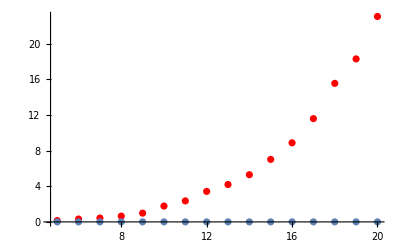

```mathematica
Show[ListPlot[timing[[All,1;;2]],PlotStyle->Red],ListPlot[timing[[All,{1,-1}]]]]
```

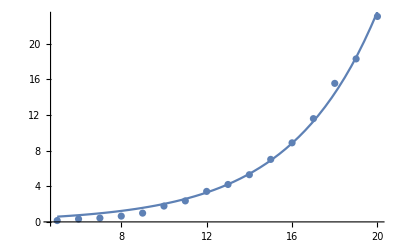

```mathematica
data = Transpose[{timing[[All,1]],timing[[All,2]]}];
fit=NonlinearModelFit[data,Exp[a +b x],{a,b},x];
Show[ListPlot[data],Plot[fit[x],{x,5,20}]]
```